```mathematica
g[p_,max_] := Product[Sin[Pi/p^k(x)],{k,0,max-1}]
```

```mathematica
g[3,2]
```

```mathematica
FindGeneratingFunction[{0,1,2,5,6,7,10,11,12,15,16,17},x]
```

(x+x^2+3 x^3)/((-1+x)^2 (1+x+x^2))

```mathematica
FindGeneratingFunction[{0,1,3,4,6,7,9,10},x]
```

(x+2 x^2)/((-1+x)^2 (1+x))

```mathematica
FindGeneratingFunction[{3,4,9,10,15,16},x]
```

1/(1+x)+(2+x)/(-1+x)^2

```mathematica
FindGeneratingFunction[{0,1,2,3,7,8,9,10,14,15,16,17,21,22,23,24,28,29,30,31},x]
```

(x (1+x+x^2+4 x^3))/((-1+x)^2 (1+x+x^2+x^3))

```mathematica
FindGeneratingFunction[{0,1,2,3,4,5,11,12,13,14,15,16,22,23,24,25,26,27,33,34,35,36,37,38,39,44,45,46,47,48,49,55,56,57,58,59,60,66,67,68,69,70,71},x]
```

FindGeneratingFunction[{0,1,2,3,4,5,11,12,13,14,15,16,22,23,24,25,26,27,33,34,35,36,37,38,39,44,45,46,47,48,49,55,56,57,58,59,60,66,67,68,69,70,71},x]

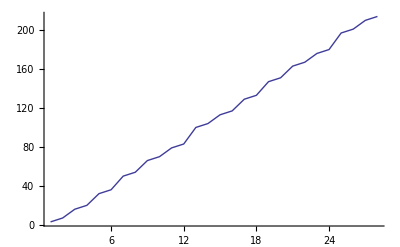

```mathematica
ListPlot[CoefficientList[Series[FindGeneratingFunction[{3,4,9,10,15,16},x] + FindGeneratingFunction[{0,1,3,4,6,7,9,10},x] + (x+x^2+ x^3+4 x^4)/((-1+x)^2 (1+x+x^2+x^3)) + (x (1+x+x^2+ x^3+ x^4+ 6 x^5))/((-1+x)^2 (1+x+x^2+x^3 + x^4+ x^5)),{x,0,27}],x], Joined->True]
```

```mathematica
CoefficientList[Series[(x (1+x+x^2+ x^3+ x^4+ 6 x^5))/((-1+x)^2 (1+x+x^2+x^3 + x^4+ x^5)),{x,0,200}],x]
```

{0,1,2,3,4,5,11,12,13,14,15,16,22,23,24,25,26,27,33,34,35,36,37,38,44,45,46,47,48,49,55,56,57,58,59,60,66,67,68,69,70,71,77,78,79,80,81,82,88,89,90,91,92,93,99,100,101,102,103,104,110,111,112,113,114,115,121,122,123,124,125,126,132,133,134,135,136,137,143,144,145,146,147,148,154,155,156,157,158,159,165,166,167,168,169,170,176,177,178,179,180,181,187,188,189,190,191,192,198,199,200,201,202,203,209,210,211,212,213,214,220,221,222,223,224,225,231,232,233,234,235,236,242,243,244,245,246,247,253,254,255,256,257,258,264,265,266,267,268,269,275,276,277,278,279,280,286,287,288,289,290,291,297,298,299,300,301,302,308,309,310,311,312,313,319,320,321,322,323,324,330,331,332,333,334,335,341,342,343,344,345,346,352,353,354,355,356,357,363,364,365}

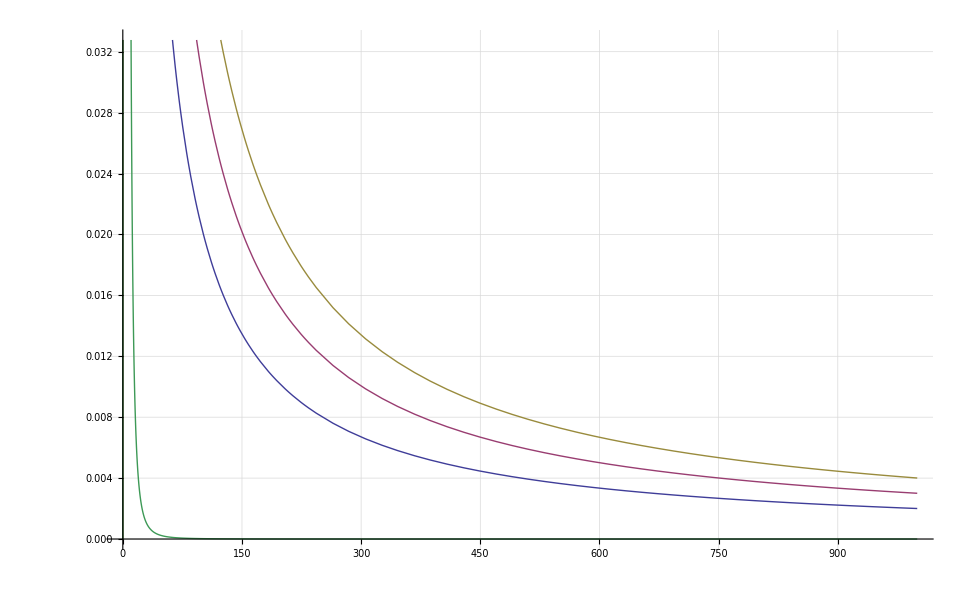

```mathematica
Plot[{(x+2 x^2)/((-1+x)^2 (1+x)) ,(x+x^2+3 x^3)/((-1+x)^2 (1+x+x^2)),(x+x^2+ x^3+4 x^4)/((-1+x)^2 (1+x+x^2+x^3)),(x+2 x^2)/((-1+x)^2 (1+x)) *(x+x^2+3 x^3)/((-1+x)^2 (1+x+x^2))*(x+x^2+ x^3+4 x^4)/((-1+x)^2 (1+x+x^2+x^3))},{x,0,1000}, GridLines->Automatic]
```

```mathematica
Series[g[3,10],x]
```

```mathematica
FullSimpliy[FindGeneratingFunction[{3,4,9,10,15,16},x] *FindGeneratingFunction[{0,1,3,4,6,7,9,10},x]]
```

FullSimpliy[((x+2 x^2) (1/(1+x)+(2+x)/(-1+x)^2))/((-1+x)^2 (1+x))]

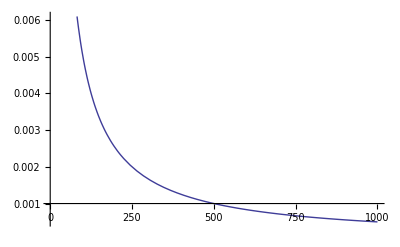

```mathematica
Plot[{Re[1/(2x)*(1-Sqrt[1-4x])]},{x,1,1000}]
```

```mathematica
Table[{x, 1/(2x)*(1-Sqrt[1-4x])},{x,1,10}]
```

{{1,1/2 (1-ⅈ √3)},{2,1/4 (1-ⅈ √7)},{3,1/6 (1-ⅈ √11)},{4,1/8 (1-ⅈ √15)},{5,1/10 (1-ⅈ √19)},{6,1/12 (1-ⅈ √23)},{7,1/14 (1-3 ⅈ √3)},{8,1/16 (1-ⅈ √31)},{9,1/18 (1-ⅈ √35)},{10,1/20 (1-ⅈ √39)}}

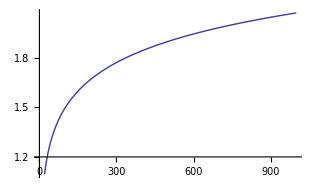

```mathematica
Plot[{Re[1/2 (√(1-4 x)+Log[-1+√(1-4 x)])]},{x,1,1000}]
```

```mathematica
Integrate[1/(1-Sqrt[1-4x]),x]
```

1/2 (√(1-4 x)+Log[-1+√(1-4 x)])